```mathematica
(*Mathematica*)
```

```mathematica
(*8 cubic polynomials*)
```

```mathematica
(* three real root cubic polynomials one negative , two positive roots, Pascal, GoldenRatio , Bombieri, ...*)
```

```mathematica
p=ExpandAll[{(x-1)^2*(x+1),(-1-x+x^2)*(x-1),1-x-2 x^2+x^3,(1-3 x^2+x^3),1-2 x-3 x^2+x^3,1- x-4 x^2+x^3,1.-4* x-4* x^2+x^3,1-2*x-5 x^2+x^3}]
```

{1-x-x^2+x^3,1-2 x^2+x^3,1-x-2 x^2+x^3,1-3 x^2+x^3,1-2 x-3 x^2+x^3,1-x-4 x^2+x^3,1.-4 x-4 x^2+x^3,1-2 x-5 x^2+x^3}

```mathematica
Table[x/.NSolve[p[[i]]==0,x],{i,Length[p]}]
```

{{-1.,1.,1.},{-0.618034,1.,1.61803},{-0.801938,0.554958,2.24698},{-0.532089,0.652704,2.87939},{-0.834243,0.34338,3.49086},{-0.588364,0.406421,4.18194},{-1.,0.208712,4.79129},{-0.634609,0.295117,5.33949}}

```mathematica
(*Largest real roots*)
```

```mathematica
a=Table[x/.NSolve[p[[i]]==0,x][[3]],{i,Length[p]}]
```

{1.,1.61803,2.24698,2.87939,3.49086,4.18194,4.79129,5.33949}

```mathematica
g1=ListPlot[Table[x/.NSolve[p[[i]]==0,x][[3]],{i,Length[p]}],PlotStyle->Red];
```

```mathematica
f[x_]=Fit[a,{1,x},x]
```

0.372476+0.626894 x

```mathematica
g2=Plot[f[x],{x,0,Length[a]+1}];
```

```mathematica
(*Linear fit plots*)
```

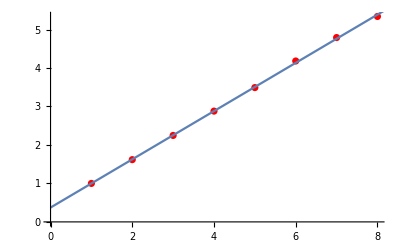

```mathematica
Show[{g1,g2}]
```

```mathematica
(* toral inverse cubic polynomials*)
```

```mathematica
q=Table[ExpandAll[x^3*(p[[i]]/.x->1/x)],{i,Length[p]}]
```

{1-x-x^2+x^3,1-2 x+x^3,1-2 x-x^2+x^3,1-3 x+x^3,1-3 x-2 x^2+x^3,1-4 x-x^2+x^3,1-4 x-4 x^2+1. x^3,1-5 x-2 x^2+x^3}

```mathematica
(* sequence of polynomial expansion*)
```

```mathematica
(*OEIS search:
1)https://oeis.org/A00452
   2)https://oeis.org/A006054
      3)https://oeis.org/A000071
         4)https://oeis.org/A076264
            5)Sorry,but the terms do not match anything in the table
               6)https://oeis.org/A364705
                 7)https://oeis.org/A099025
                    8)Sorry,but the terms do not match anything in the table.
 *)
```

```mathematica
Table[Table[SeriesCoefficient[Series[1/q[[i]],{x,0,30}],m],{m,30}],{i,Length[q]}]
```

{{1,2,2,3,3,4,4,5,5,6,6,7,7,8,8,9,9,10,10,11,11,12,12,13,13,14,14,15,15,16},{2,4,7,12,20,33,54,88,143,232,376,609,986,1596,2583,4180,6764,10945,17710,28656,46367,75024,121392,196417,317810,514228,832039,1346268,2178308,3524577},{2,5,11,25,56,126,283,636,1429,3211,7215,16212,36428,81853,183922,413269,928607,2086561,4688460,10534874,23671647,53189708,119516189,268550439,603427359,1355888968,3046654856,6845771321,15382308530,34563733525},{3,9,26,75,216,622,1791,5157,14849,42756,123111,354484,1020696,2938977,8462447,24366645,70160958,202020427,581694636,1674922950,4822748423,13886550633,39984728949,115131438424,331507764639,954538564968,2748484256480,7913945004801,22787296449435,65613405091825},{3,11,38,133,464,1620,5655,19741,68913,240566,839783,2931568,10233704,35724465,124709235,435342931,1519722798,5305145021,18519537728,64649180428,225681471719,787823238285,2750183477865,9600515438446,33514090032783,116993117497376,408407017119248,1425693196319713,4976900505700259,17373680892620955},{4,17,71,297,1242,5194,21721,90836,379871,1588599,6643431,27782452,116184640,485877581,2031912512,8497342989,35535406887,148607058025,621466295998,2598936835130,10868606578493,45451896853104,190077257155779,794892318897727,3324194635893583,13901593605316280,58135676738260976,243120105922466601,1016714506822811100,4251842456475450025},{4,20,95.,456.,2184.,10465.,50140.,240236.,1.15104×10^6,5.51496×10^6,2.64238×10^7,1.26604×10^8,6.06595×10^8,2.90637×10^9,1.39253×10^10,6.672×10^10,3.19675×10^11,1.53165×10^12,7.33859×10^12,3.51613×10^13,1.68468×10^14,8.07178×10^14,3.86742×10^15,1.85299×10^16,8.87823×10^16,4.25381×10^17,2.03813×10^18,9.76524×10^18,4.67881×10^19,2.24175×10^20},{5,27,144,769,4106,21924,117063,625057,3337487,17820486,95152347,508065220,2712810308,14485029633,77342703561,412970766763,2205054211304,11773869886485,62866487088270,335675121003016,1792334709305135,9570157301443437,51099780804824439,272846883917703934,1456863823896725111,7778913106514208984,41535446296446791208,221778193871365648897,1184182948843207617917,6322935685662322596171}}

```mathematica
(*end*)
```

```mathematica
(* mathematica*)
Clear[cr,cols,cr2,cr3,cr4,firstCols,s,s0]
allColors=ColorData["Legacy"][[3,1]];
firstCols={"White","AliceBlue","LightBlue" ,"Cyan","ManganeseBlue","DodgerBlue" ,"Blue","Magenta","Purple","Pink","Tomato","Red","DarkOrange","Orange","DeepNaplesYellow","Gold","Banana","Yellow","LightYellow","Orange","Pink","LightPink","Yellow","LightYellow","LightPink","White","DeepNaplesYellow", "Orange","DarkOrange","Tomato","Red","Tomato","Pink","LightPink","DeepNaplesYellow", "Orange","DarkOrange","Tomato","White","Pink","Banana","LightBlue","DodgerBlue","Cyan","White","Purple","DarkOrchid","Magenta","ManganeseBlue","DeepNaplesYellow", "Orange","DarkOrange","Tomato","GoldOchre","LightPink","Magenta","Green","DarkOrchid","LightSalmon","LightPink","Sienna","Green","Mint","DarkSlateGray","ManganeseBlue","SlateGray","DarkOrange","MistyRose","DeepNaplesYellow","GoldOchre","SapGreen","Yellow","Yellow","Tomato","DeepNaplesYellow","DodgerBlue","Cyan","Red","Blue","DeepNaplesYellow","Green","Magenta","DarkOrchid","LightSalmon","LightPink","Sienna","Green","Mint","DarkSlateGray","ManganeseBlue","SlateGray","DarkOrange","MistyRose","DeepNaplesYellow","GoldOchre","SapGreen","Yellow","LimeGreen"};
cols=ColorData["Legacy",#]&/@Join[firstCols,Complement[allColors,firstCols]];
rotate[theta_]:={{Cos[theta],-Sin[theta]},{Sin[theta],Cos[theta]}};
cr[n_]:=cr[n]=cols[[n]];
cr2[n_]:=cr2[n]=cols[[n+4]];
cr3[n_]:=cr3[n]=cols[[n+8]];
cr4[n_]:=cr4[n]=cols[[n+12]];
cr5[n_]:=cr5[n]=cols[[n+16]]
Clear[mu,a,b,A,B]
```

```mathematica
NSolve[1-2 x-5 x^2+x^3==0,x]
```

{{x→-0.634609},{x→0.295117},{x→5.33949}}

```mathematica
r[i_]:=x/.NSolve[1-2 x-5 x^2+x^3==0,x][[i]]
```

```mathematica
s[1]=N[{{r[3],12},{0,1/r[1]}}]/Sqrt[Det[N[{{r[3],12},{0,1/r[1]}}]]]
s[2]=N[{{1,0},{12*I/(r[3]^2-1),1}}]
s[3]=Inverse[s[1]]
s[4]=Inverse[s[2]]
```

{{0.-1.84079 ⅈ,0.-4.13699 ⅈ},{0.+0. ⅈ,0.+0.543246 ⅈ}}

{{1.,0.},{0.+0.436202 ⅈ,1.}}

{{0.+0.543246 ⅈ,0.+4.13699 ⅈ},{0.+0. ⅈ,0.-1.84079 ⅈ}}

{{1.+0. ⅈ,0.+0. ⅈ},{0.-0.436202 ⅈ,1.+0. ⅈ}}

```mathematica
qf=N[rotate[Pi/4]];qfi=Inverse[qf]
s0=N[{{1,-I},{-I,1}}/Sqrt[2]];s1=Inverse[s0];
```

{{0.707107,0.707107},{-0.707107,0.707107}}

```mathematica
{a,b,A,B}=Table[N[qf.s[i].qfi],{i,4}]
```

{{{0.+1.41973 ⅈ,0.-3.26051 ⅈ},{0.+0.876479 ⅈ,0.-2.71726 ⅈ}},{{1.-0.218101 ⅈ,0.-0.218101 ⅈ},{0.+0.218101 ⅈ,1.+0.218101 ⅈ}},{{0.-2.71726 ⅈ,0.+3.26051 ⅈ},{0.-0.876479 ⅈ,0.+1.41973 ⅈ}},{{1.+0.218101 ⅈ,0.+0.218101 ⅈ},{0.-0.218101 ⅈ,1.-0.218101 ⅈ}}}

```mathematica
Det[a]
Tr[a]
Det[b]
Tr[b]
Det[A]
Tr[A]
Det[B]
Tr[B]
```

1.+0. ⅈ

0.-1.29754 ⅈ

1.+0. ⅈ

2.+0. ⅈ

1.+0. ⅈ

0.-1.29754 ⅈ

1.+0. ⅈ

2.+0. ⅈ

```mathematica
Affine[{z1_,z2_}]:=0.000001 Round[(z1/z2)/0.000001];
Children[{z_,n_}]:={Affine[{a,b,A,B}[[#]].{z,1}],#}&/@Delete[Range[4],{3,4,1,2}[[n]]];
aa1={Re[#[[1]]],Im[#[[1]]]}&/@Nest[Union[Flatten[Children/@#,1]]&,ParallelTable[{Affine[{a,b,A,B}[[i]].{0,1}],i},{i,1,4}],11];
ll=Length[aa1]
Last[aa1]
aa=aa1;
```

708579

{4.44572,0.112732}

```mathematica
g0=ListPlot[aa,AspectRatio->Automatic,ColorFunction->"Rainbow",PlotStyle->{PointSize[0.001]},ImageSize->2000,PlotRange->{{-2,6},{-8/2,8/2}},Axes->False];
```

```mathematica
dlst=Table[1+Mod[Floor[1+(1+Floor[12*Norm[aa[[i]]]])/(Abs[Cos[Arg[aa[[i,1]]+I*aa[[i,2]]]]]+Abs[Sin[Arg[aa[[i,1]]+I*aa[[i,2]]]]])],Length[cols]],{i,Length[aa]}];
Min[dlst]
Max[dlst]
ptlst=Point[Developer`ToPackedArray[aa],VertexColors->Developer`ToPackedArray[cr/@dlst]];
```

9

54

```mathematica
g2=Graphics[{PointSize[.001],ptlst},AspectRatio->Automatic,ImageSize->2000,PlotRange->{{-2,6},{-8/2,8/2}},Background->Black];
```

```mathematica
(* end limit set*)
```

```mathematica
(*Perpendicular Hermetian inversion conformal map: z*Conjugate[z]/Abs[z]^2=1*)
```

```mathematica
bb=Delete[Reverse[Union[Table[{aa[[i,1]],-aa[[i,2]]}/(aa[[i,1]]^2+aa[[i,2]]^2),{i,Length[aa]}]]],1];
```

```mathematica
g1=ListPlot[bb,AspectRatio->Automatic,ColorFunction->"Rainbow",PlotStyle->{PointSize[0.001]},ImageSize->2000,PlotRange->{{-20,20},{-20,20}}/18];
```

```mathematica
ptlst1a=Point[Developer`ToPackedArray[bb],VertexColors->Developer`ToPackedArray[cr/@dlst]];
```

```mathematica
g5=Graphics[{PointSize[.001],ptlst1a},AspectRatio->Automatic,ImageSize->2000,PlotRange->{{-20,20},{-20,20}}/18,Background->Black];
```

```mathematica
(* Half plane to disk conformal map*)

bb1=Delete[Union[ParallelTable[{-(Im[-1/((1+aa⟦i,1⟧)^2+aa⟦i,2⟧^2)+aa⟦i,1⟧^2/((1+aa⟦i,1⟧)^2+aa⟦i,2⟧^2)+aa⟦i,2⟧^2/((1+aa⟦i,1⟧)^2+aa⟦i,2⟧^2)]+2 Re[aa⟦i,2⟧/((1+aa⟦i,1⟧)^2+aa⟦i,2⟧^2)]),-2 Im[aa⟦i,2⟧/((1+aa⟦i,1⟧)^2+aa⟦i,2⟧^2)]+Re[-1/((1+aa⟦i,1⟧)^2+aa⟦i,2⟧^2)+aa⟦i,1⟧^2/((1+aa⟦i,1⟧)^2+aa⟦i,2⟧^2)+aa⟦i,2⟧^2/((1+aa⟦i,1⟧)^2+aa⟦i,2⟧^2)]},{i,Length[aa]}]],Length[Union[ParallelTable[{-(Im[-1/((1+aa⟦i,1⟧)^2+aa⟦i,2⟧^2)+aa⟦i,1⟧^2/((1+aa⟦i,1⟧)^2+aa⟦i,2⟧^2)+aa⟦i,2⟧^2/((1+aa⟦i,1⟧)^2+aa⟦i,2⟧^2)]+2 Re[aa⟦i,2⟧/((1+aa⟦i,1⟧)^2+aa⟦i,2⟧^2)]),-2 Im[aa⟦i,2⟧/((1+aa⟦i,1⟧)^2+aa⟦i,2⟧^2)]+Re[-1/((1+aa⟦i,1⟧)^2+aa⟦i,2⟧^2)+aa⟦i,1⟧^2/((1+aa⟦i,1⟧)^2+aa⟦i,2⟧^2)+aa⟦i,2⟧^2/((1+aa⟦i,1⟧)^2+aa⟦i,2⟧^2)]},{i,Length[aa]}]]]];
```

```mathematica
ListPlot[bb1,PlotStyle->{{Yellow,PointSize[0.001]},{Orange,PointSize[0.001]}},ImageSize->1000,Axes->True,PlotRange->{-50,50}/10];
```

```mathematica
ptlst3:=Point[Developer`ToPackedArray[bb1],VertexColors->Developer`ToPackedArray[cr/@dlst]];

g3=Rasterize[Graphics[{PointSize[.001],ptlst3(*,ptlst2*)},AspectRatio->Automatic,ImageSize->2000,Background->Black,PlotRange->2],RasterSize->2000,ImageSize->2000];
```

```mathematica
cc1=ParallelTable[{2*aa[[i,1]],2*aa[[i,2]],(1-aa[[i]].aa[[i]])}/(1+aa[[i]].aa[[i]]),{i,Length[aa]}];
```

```mathematica
ptlst5a=Point[Developer`ToPackedArray[cc1],VertexColors->Developer`ToPackedArray[cr/@dlst]];
```

```mathematica
g4=Rasterize[Graphics3D[{PointSize[.001],ptlst5a},AspectRatio->Automatic,ImageSize->2000,PlotRange->All,Background->Black,Boxed->False,ViewPoint->{2.1,2.1,2.1}],RasterSize->2000,ImageSize->2000];
```

```mathematica
Export["Nylander_2group_Bombieri_extended_cubic_Quasiconformal45_limitset_11.jpg",GraphicsGrid[{{g0,g2},{g1,g5},{g3,g4}},ImageSize->6000]]
```

Nylander_2group_Bombieri_extended_cubic_Quasiconformal45_limitset_11.jpg

```mathematica
(*end*)
```

Lookup::invrl: The argument Missing[NotAvailable] is not a valid Association or a list of rules.